## 1. Solving TOV equations.

### 1.1 Equation of state:

#### 1.1.1 Relativistic Case (pure NS)

Let’s try first just this one: relativistic case

```mathematica
Pressure R[ϵ_]:=ϵ/3;
Density R[p_]:=3p;
```

#### 1.1.2 Non Relativistic Case (pure NS)

Pressure and density take the following form

```mathematica
ϵ(P) = 5 (m/(15 π^2 λ^3))^(2/5)P^(3/5)
```

with m, λ of the gas we are considering, let’s say neutrons only, then

```mathematica
m=1.67 10^-24;
c = 2.99792458 10^10;
lambda=2.1 10^-14;
k =5((m c^2)/(15 π^2 lambda^3))^(0.4);
(*   Functions:    *)
Density NR[p_]:=k p^0.6
Pressure NR[ϵ_]:= (ϵ/k)^5/3
```

#### 1.1.3 Whole Range Neutron Star (Pure NS)

We need first to define density and pressure as function of non-dimensional fermi momentum

```mathematica
n = m c^2/(Pi^2*lambda^3);
epsilon[z_]:=n/8 ((2z^3+z)Sqrt[1+z^2]-ArcSinh[z])
pressure[z_]:=n/8((2z^3 /3-z)Sqrt[1+z^2]+ArcSinh[z])
```

now, we create a table of data (p, ϵ):

```mathematica
d1 = Table[{pressure[z],epsilon[z]},{z,10.^-3,10^-2,10^-5}];
d2 =Table[{pressure[z],epsilon[z]},{z,10.^-2,10^-1,10^-4}];
d3=Table[{pressure[z],epsilon[z]},{z,10.^-1,10^0,10^-3}];
d4=Table[{pressure[z],epsilon[z]},{z,10.^0,10^1,10^-2}];
d5=Table[{pressure[z],epsilon[z]},{z,10.^1,10^2,10^-1}];
d6=Table[{pressure[z],epsilon[z]},{z,10.^2,10^3,10^0}];
```

```mathematica
density n=Union[d1,d2,d3,d4,d5,d6];
Density NS = Interpolation[density n,InterpolationOrder->100];
```

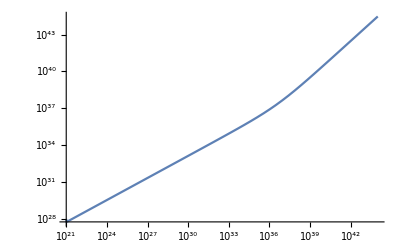

```mathematica
LogLogPlot[Density NS[x],{x,10^21,10^44}]
```

Now, let’s build the function for the whole range as a picewise function taking the R and NR approx,

```mathematica
pw=Piecewise[{{Density NR[x], 0≤  x<10^23}, {Density NS[x],10^23≤ x≤ 10^45},{Density R[x],x>10^45}}];
dener[p_]:=pw/.x-> p
```

#### Constants

We need to declare the following constants

```mathematica
G = 6.673 10^-8;
Subscript[M, sol]=1.9891 10^33;
c = 2.99792458 10^10;
α=G Subscript[M, sol]/(10^5 c^2);
Subscript[E0, sol]= Subscript[M, sol] c^2;
km3 = (10.0^5)^3;
rmin = 0.001;
rmax = 350;
densup = 7.86;
```

The numerical values of the constants to non-dimensionalise the equations are:

```mathematica
beta[Pc_]:=4 Pi Pc km3 /Subscript[E0, sol];
β =beta[3 10^34];
```

```mathematica
{α,β}
```

{1.47685,0.000210879}

Now we can proceed to do the numerical integration

#### Newton Equations:

We solve first this simple case.

```mathematica
Pc = 3.3 10^34;
Do[
{solution = NDSolve[{p'[r]== If[p[r]>0,-(α dener[p[r]*Pc]*M[r])/(Pc r^2),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],p[rmin]==1,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
mass ad[x_]:=M[x]/.solution[[1]];
pressure ad[x_]:=p[x]/.solution[[1]];
If[pressure ad[x]> 0,Print[0],Print[1]](*;Print[rad, " ", mass ad[rad], " " , pressure ad[rad]*Pc," ", dener[pressure ad[rad] Pc] ]*)},
{rad,10,20,.1}]
```

```mathematica
rstep=0.001;
While[dener[pressure ad[radius]]/c^2≥densup,
radius=radius+rstep;
Print[radius,"\t",dener[pressure ad[radius]]]]
```

capR

#### TOV Equations:

```mathematica
Pc = 3.3 10^34;
Do[{solution = NDSolve[{p'[r]== If[p[r]>0,-α*(M[r] +(4 π (Pc km3)/Subscript[E0, sol])r^3 p[r])( (dener[p[r]*Pc]*M[r])/(Pc r^2)+p[r])/(r(r - 2 α M[r])),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],p[rmin]==1,M[rmin]==0.0},{p,M},{r,rmin,40},MaxSteps->Infinity];
mass ad[x_]:=M[x]/.solution[[1]];
pressure ad[x_]:=p[x]/.solution[[1]];
Print[rad, " ", mass ad[rad], " " , pressure ad[rad]*Pc," ", dener[pressure ad[rad] Pc] ]},{rad,5,40}]
```

5 0.217553 3.15628×10^34 7.33815×10^35

6 0.372846 3.08451×10^34 7.23012×10^35

7 0.585919 2.99373×10^34 7.09227×10^35

8 0.863308 2.88095×10^34 6.91908×10^35

9 1.20961 2.74247×10^34 6.70329×10^35

10 1.62675 2.57354×10^34 6.43508×10^35

11 2.11294 2.3681×10^34 6.10082×10^35

12 2.66111 2.1184×10^34 5.68106×10^35

13 3.25653 1.815×10^34 5.14767×10^35

14 3.8731 1.44892×10^34 4.46127×10^35

15 4.4686 1.02264×10^34 3.57984×10^35

16 4.98395 5.86817×10^33 2.52733×10^35

17 5.36791 2.66257×10^33 1.54739×10^35

18 5.62527 1.13847×10^33 9.17496×10^34

19 5.80108 5.46053×10^32 5.85592×10^34

20 5.93118 3.01428×10^32 4.07895×10^34

21 6.03494 1.86407×10^32 3.04696×10^34

22 6.12252 1.25624×10^32 2.39901×10^34

23 6.1996 9.03888×10^31 1.96577×10^34

24 6.2696 6.84299×10^31 1.66138×10^34

25 6.33473 5.39375×10^31 1.43892×10^34

26 6.39645 4.39201×10^31 1.27107×10^34

27 6.45582 3.6728×10^31 1.14105×10^34

28 6.51361 3.1398×10^31 1.03807×10^34

29 6.5704 2.73409×10^31 9.54975×10^33

30 6.62665 2.41813×10^31 8.86827×10^33

31 6.68272 2.16714×10^31 8.30143×10^33

32 6.7389 1.96429×10^31 7.82405×10^33

33 6.79543 1.79784×10^31 7.41755×10^33

34 6.85252 1.65941×10^31 7.06799×10^33

35 6.91035 1.54289×10^31 6.76472×10^33

36 6.96907 1.44375×10^31 6.49948×10^33

37 7.02881 1.35859×10^31 6.2658×10^33

38 7.0897 1.28479×10^31 6.05854×10^33

39 7.15184 1.22031×10^31 5.87359×10^33

40 7.21533 1.16357×10^31 5.70759×10^33